```mathematica
raw = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/output_data.json"];
data =Association[#]&/@raw;
```

```mathematica
data[[1]]//Keys
```

{QA10361kG,QA10371kG,norm_emit_x,norm_emit_y,maximizeMe}

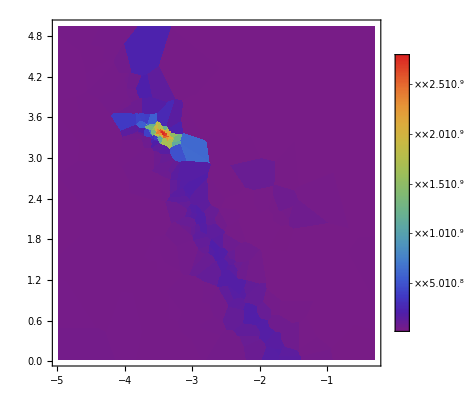

```mathematica
ListDensityPlot[
{
#QA10361kG,
#QA10371kG,
#maximizeMe
}&/@data,
InterpolationOrder->0,
ColorFunction->"Rainbow",
PlotLegends->Placed[Automatic,{0.85,0.5}],
LabelStyle->15,
PlotRangePadding->None
]
```